Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

8 - 13 Find the adjacency matrix of the given graph or digraph.

9.

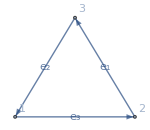

```mathematica
g1=Graph[{Labeled[1->2,"e_3"],Labeled[2->3,"e_1"],Labeled[3->1,"e_2"]},VertexLabels->"Name",ImageSize->150]
```

```mathematica
ceg=AdjacencyMatrix[g1]//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)

11.

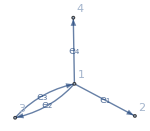

```mathematica
g2=Graph[{Labeled[1->2,"e_1"],Labeled[1->3,"e_2"],Labeled[3->1,"e_3"],Labeled[1->4,"e_4"]},VertexLabels->"Name",ImageSize->150]
```

```mathematica
ceh=AdjacencyMatrix[g2]//MatrixForm
```

(0 | 1 | 1 | 1
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0)

13.

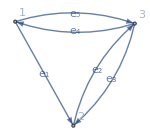

```mathematica
g3=Graph[{Labeled[1->2,"e_1"],Labeled[1->3,"e_5"],Labeled[3->1,"e_4"],Labeled[2->3,"e_2"],Labeled[3->2,"e_3"]},VertexLabels->"Name",ImageSize->150]
```

```mathematica
cei=AdjacencyMatrix[g3]//MatrixForm
```

(0 | 1 | 1
0 | 0 | 1
1 | 1 | 0)

14 - 15 Sketch the graph for the given adjacency matrix.

15.

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
cej={{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}
```

{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}

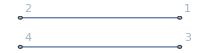

```mathematica
AdjacencyGraph[cej,ImageSize->200,VertexLabels->"Name"]
```

The relationship between vertices in the above sketch is comparable to that of the text, except mirrored.

17.  In what case are all the off-diagonal entries of the adjacency matrix of a graph G equal to one?

```mathematica
cek=({{0, 1, 1, 1}, {1, 0, 1, 1}, {1, 1, 0, 1}, {1, 1, 1, 0}})
```

{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}

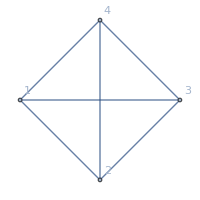

```mathematica
AdjacencyGraph[cek,ImageSize->200,VertexLabels->"Name"]
```

The example I made suggests that each pair of vertices is joined by an edge, i.e. it is a complete graph.

19.  Incidence matrix B̃ of a digraph. The definition is B̃ = [b_(j k)], where
(b̃)_(j k)=Piecewise[{{-1, if edge e_k leaves vertex j,}, {1, if edge e_k enters vertex j,}, {0, otherwise}}]
Find the incidence matrix of the digraph in problem 11.

I find that getting the neat table of edges and vertices requires imitating the exact steps shown in the documentation for IncidenceMatrix. Specifically, if the MatrixForm of g2 is not shielded by a buffer cell from the call for TableForm, then TableForm will just repeat the MatrixForm, as illogical as that seems.

```mathematica
Clear["Global`*"]
```

```mathematica
g2=Graph[{Labeled[1->2,"e_1"],Labeled[1->3,"e_2"],Labeled[3->1,"e_3"],Labeled[1->4,"e_4"]},VertexLabels->"Name",ImageSize->150]
```

-Graphics-

```mathematica
im1=IncidenceMatrix[g2]//MatrixForm
```

(-1 | -1 | 1 | -1
1 | 0 | 0 | 0
0 | 1 | -1 | 0
0 | 0 | 0 | 1)

```mathematica
im1=IncidenceMatrix[g2=Graph[{Labeled[1->2,"e_1"],Labeled[1->3,"e_2"],Labeled[3->1,"e_3"],Labeled[1->4,"e_4"]},VertexLabels->"Name",ImageSize->150]]
```

SparseArray[<8>, {4, 4}]

Getting a table which looks a little like the text answer.

```mathematica
tek=TableForm[Normal[im1],TableHeadings->{VertexList[g2],EdgeList[g2]}]
```

| 1->2 | 1->3 | 3->1 | 1->4
1 | -1 | -1 | 1 | -1
2 | 1 | 0 | 0 | 0
3 | 0 | 1 | -1 | 0
4 | 0 | 0 | 0 | 1